```mathematica
ClearAll["Global`*"]
```

```mathematica
f=V0*((a/x)^12-2*(a/x)^6);
```

```mathematica
Integrate[E^(-f)*x^2,{x,a-0.01,a+0.01}]
```

∫_(-0.01+a)^(0.01+a) ⅇ^(-V0 (a^12/x^12-(2 a^6)/x^6)) x^2ⅆx

```mathematica
Solve[D[f,x]==0,x]
```

{{x→-a},{x→a},{x→-(-1)^(1/3) a},{x→(-1)^(1/3) a},{x→-(-1)^(2/3) a},{x→(-1)^(2/3) a}}

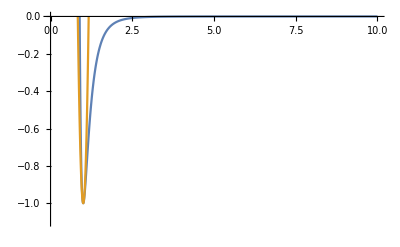

```mathematica
V0=1;a=1;Plot[{f,g},{x,0,10},PlotRange->{-1.1,0}]
```

```mathematica
Series[f,{x,a,3}]
```

-V0+(36 V0 (x-a)^2)/a^2-(252 V0 (x-a)^3)/a^3+O[x-a]^4

```mathematica
g=-V0+(36 V0 (x-a)^2)/a^2;
```

```mathematica
Integrate[E^(-g*B)*x^3*g,{x,-∞,∞},Assumptions->{V0∈Reals,a∈Reals,a>0,V0>0,B∈Reals,B>0}]
```

-(a^4 ⅇ^(B V0) √π V0 (-3+2 B V0 (-11+24 B V0)))/(288 (B V0)^(5/2))

```mathematica
Solve[g==0,x]
```

{{x→(5 a)/6},{x→(7 a)/6}}

```mathematica
Error[x_] := Abs[f-g]
```

```mathematica
Abs[V0+V0 (a^12/x^12-(2 a^6)/x^6)-(36 V0 (-a+x)^2)/a^2]
```

Abs[V0+V0 (a^12/x^12-(2 a^6)/x^6)-(36 V0 (-a+x)^2)/a^2]

{}

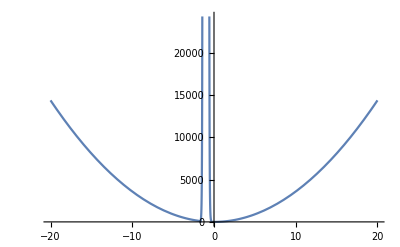

```mathematica
V0=1;a=1;Plot[Abs[Error/.x->(a+e)],{e,-20,20}]
```

```mathematica
Solve[Abs[V0+V0 (a^12/(a+e)^12-(2 a^6)/(a+e)^6)-(36 V0 (e)^2)/a^2]==0.01,e]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{e→Root[30+2.621376×10^10 a^3 1 #1^25+3.57624×10^9 a^2 V0^2 #1^26+3.1104×10^8 a V0^2 #1^27+1.296×10^7 V0^2 #1^28&,1]},{e→Root[1&,2]},24,{e→1},{e→Root[32+1+1.296×10^7 V0^2 #1^28&,28]}}
 |  |  |  |

```mathematica
Error[a+e]
```

Abs[V0+V0 (a^12/x^12-(2 a^6)/x^6)-(36 V0 (-a+x)^2)/a^2]

```mathematica
Solve[x^12*(-1+0.01/V0)+2*a^6*x^6-a^12==0,x]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→-1.4678 (-(10. a^6)/(-100.+1/V0)-(1. a^6)/((-100.+1/V0) √V0))^(1/6)},{x→(-0.7339-1.27115 ⅈ) (-(10. a^6)/(-100.+1/V0)-(1. a^6)/((-100.+1/V0) √V0))^(1/6)},{x→(-0.7339+1.27115 ⅈ) (-(10. a^6)/(-100.+1/V0)-(1. a^6)/((-100.+1/V0) √V0))^(1/6)},{x→(0.7339-1.27115 ⅈ) (-(10. a^6)/(-100.+1/V0)-(1. a^6)/((-100.+1/V0) √V0))^(1/6)},{x→(0.7339+1.27115 ⅈ) (-(10. a^6)/(-100.+1/V0)-(1. a^6)/((-100.+1/V0) √V0))^(1/6)},{x→1.4678 (-(10. a^6)/(-100.+1/V0)-(1. a^6)/((-100.+1/V0) √V0))^(1/6)},{x→-1.4678 (-(10. a^6)/(-100.+1/V0)+a^6/((-100.+1/V0) √V0))^(1/6)},{x→(-0.7339-1.27115 ⅈ) (-(10. a^6)/(-100.+1/V0)+a^6/((-100.+1/V0) √V0))^(1/6)},{x→(-0.7339+1.27115 ⅈ) (-(10. a^6)/(-100.+1/V0)+a^6/((-100.+1/V0) √V0))^(1/6)},{x→(0.7339-1.27115 ⅈ) (-(10. a^6)/(-100.+1/V0)+a^6/((-100.+1/V0) √V0))^(1/6)},{x→(0.7339+1.27115 ⅈ) (-(10. a^6)/(-100.+1/V0)+a^6/((-100.+1/V0) √V0))^(1/6)},{x→1.4678 (-(10. a^6)/(-100.+1/V0)+a^6/((-100.+1/V0) √V0))^(1/6)}}

```mathematica
Simplify[1.4677992676220695 (-(10. a^6)/(-100.+1/V0)-(1. a^6)/((-100.+1/V0) √V0))^(1/6),Assumptions->{a>0,V0>0}]
```

1. a ((0.1 √V0+1. V0)/(-0.01+1. V0))^(1/6)

```mathematica
Simplify[1.4677992676220695 (-(10. a^6)/(-100.+1/V0)+a^6/((-100.+1/V0) √V0))^(1/6),Assumptions->a>0]
```

1. a ((0.1 √V0-1. V0)/(0.01-1. V0))^(1/6)

```mathematica
Integrate[E^(-(36 V0*B* (x-a)^2)/a^2)*x^2,{x,a -0.1,a +0.1}]
```

-(0.00277778 a^2 ⅇ^(-(0.36 B V0)/a^2))/(B V0)+(0.295409 a^3 (0.0138889+1. B V0) Erf[(0.6 √B √V0)/a])/(B^(3/2) V0^(3/2))

```mathematica
h=-(a^4 ⅇ^(B V0) √π V0 (-3+2 B V0 (-11+24 B V0)))/(288 (B V0)^(5/2))
```

-(a^4 ⅇ^(B V0) √π V0 (-3+2 B V0 (-11+24 B V0)))/(288 (B V0)^(5/2))

```mathematica
Expand[h]
```

-(a^4 ⅇ^(B V0) √π √(B V0))/(6 B)+(a^4 ⅇ^(B V0) √π √(B V0))/(96 B^3 V0^2)+(11 a^4 ⅇ^(B V0) √π √(B V0))/(144 B^2 V0)

```mathematica
B=1/(T*kb)
```

1/(kb T)

```mathematica
h
```

-(a^4 ⅇ^(V0/(kb T)) √π V0 (-3+(2 V0 (-11+(24 V0)/(kb T)))/(kb T)))/(288 (V0/(kb T))^(5/2))

```mathematica
Simplify[D[h,T]/a]
```

(a^3 ⅇ^(V0/(kb T)) kb √π (V0/(kb T))^(3/2) (15 kb^3 T^3+60 kb^2 T^2 V0-92 kb T V0^2+96 V0^3))/(576 V0^3)

Taylor expansion e^(-B*V_0*((a/x )^12 - 2( a/x )^6)) around x=a

WolframAlphaQueryResults

```mathematica
WolframAlpha["Taylor expansion e^(-B*V_0*((a/x )^12 - 2( a/x )^6)) around x=a",{{"SeriesExpansionAtX =A",1},"Output"}]
```

HoldComplete[ⅇ^(B V_0)-((36 B ⅇ^(B V_0) V_0) (x-a)^2)/a^2+((252 B ⅇ^(B V_0) V_0) (x-a)^3)/a^3+((3 B ⅇ^(B V_0) V_0 (-371+216 B V_0)) (x-a)^4)/a^4-((168 B ⅇ^(B V_0) V_0 (-23+54 B V_0)) (x-a)^5)/a^5+O[x-a]^6]

```mathematica
Simplify[Integrate[(ⅇ^(B Subscript[V, 0])-(36 (x-a)^2 (B Subscript[V, 0] ⅇ^(B Subscript[V, 0])))/a^2+(252 B Subscript[V, 0] (x-a)^3 ⅇ^(B Subscript[V, 0]))/a^3)*x^3,{x,a-c,a+c}]]
```

```mathematica
(ⅇ^(B Subscript[V, 0]) (2 a^4 c (a^2)))/a^3
```